## Bayesian Statistics, Assignment for Friday, Nov. 8

## Reading

Finish Chapter 9. To be frank, Chapter 9 is bugging me. Too much jargon! You can skim the jargon for now if you can still understand the authors’ point. The principles are beautifully simple!

## Overview

In Chapter 9, we still have this version of Bayes Theorem, just as we had in Chapter 8, and as I derived in my handout:

P(m^*|data)Δ m^*=(P(data|m^*)P(m^*)Δ m^*)/(∫_μ_min^μ_max P(data|m)P(m)dm)

This time I called the model parameter m instead of a, but that is a trivial change that shouldn’t bother you. Also, I have emphasized a few times that the m in the numerator is not the same as the integration variable m in the denominator and for that reason, I gave it its own name m^*. But let’s be a little less pedantic and assume we can drop the asterisks in the numerator without confusion. Then:

P(m|data)Δm=(P(data|m)P(m)Δm)/(∫_m_min^m_max P(data|m)P(m)dm)

Also, I have repeatedly emphasized that the probability of getting exactly m is zero and you have to multiply by a range of m, which I called  Δm, to get something interpretable as a probability. But that appears on both sides of the equation, and perhaps we now have enough intuition to cancel it off and to later remember when it might need to be reintroduced. Canceling it off, we have:

P(m|data)=(P(data|m)P(m))/(∫_m_min^m_max P(data|m)P(m)dm)

The only new thing in Chapter 9, when compared with Chapter 8,  is that not only is the model parameter continuous (“a continuum of hypotheses”) but the data is continuous too!! Think back to the mug breakage example. An observation could be something like 6 mugs were broken last week. Or it could be that 4 mugs were broken last week. It could not be that 4.351 mugs were broken last week. So in Chapter 8, the observations took on discrete values. In the problem illustrating Chapter 9 below, the observation (the survival time) can be any number.

## For Problem Set 12 — The Bacterium Lifetime Problem

Operationally, you understand Chapter 9 if you can do problems like this one (in your sleep, or at least with your eyes closed), although we might still have some work left to do to absorb all of Donovan and Mickey’s notation and jargon. Knowing the jargon will undoubtedly be useful when it comes time to understand later chapters.

### Description of the Prior and the Data

Imagine you have studied the literature on bacteria, and for several species of bacteria similar to the bacteria that you have collected three things are true: (1) the mean survival times for any particular species are Gaussian distributed; (2) the  bacteria have a mean survival time m of between 4 and 6 hours; and (3) that all species have a standard deviation σ=0.5 hours. The last of the three assumptions is obviously the most restrictive and contrived, but later we can show you how to relax it too.

Let’s graph the prior. Within the range, 4 to 6 hours, you have no further information as to any part of the range being more favored than another. Therefore, the prior, P(m) looks like this:

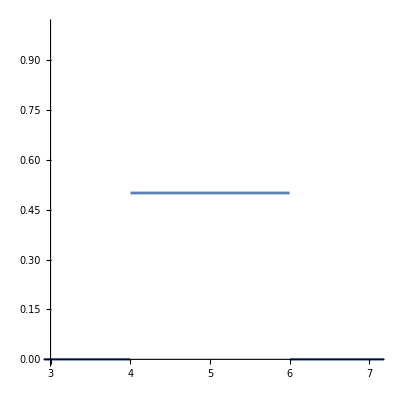

```mathematica
prior[m_]:=If[4<=m<=6, 1/(4-2),0];
Plot[prior[m],{m, 0, 8}, PlotRange->{{3, 7.1},{0,1.0}}, AspectRatio->1]
```

You isolate a single bacterium from your collection and measure its survival time as 4.7 hours. That will be your data.

### Step 1 — Computing the Likelihood Function

By assumption σ is known. Act as if μ were also known. (Remember the likelihood is P(data|m). That means we are supposed to pretend that m is given.)

(a) Write down the probability of observing a survival time of 3.6 hours. THIS IS A TRICK QUESTION! The probability of observing exactly 3.6 hours is 0 because it could have been 3.61 hours or 3.601 hours, or 3.5999 hours. So write down 0 as your answer.

(b) So of course, we mean observing a survival time x=3.6 hours plus a little range on either side of that whose total width we will just call Δx. Write down that probability. You may have to remind yourself the formula for the Gaussian distribution. It was at the top of p. 73 of Young. For your convenience, here is the top of p. 73:

You are just being asked to plug x=3.6 into this formula and then to multiply the whole formula by Δx. The result we are now thinking of as if it were a function of m rather than as a function of x, which is why Donovan and Mickey are giving it a new name in their Eq 9.46 on p. 128 and their new symbol is a curly-L.


(c) NOTICE THAT YOUNG, being an old guy like me, does not find it necessary to put in the gratuitous parenthesis around 2 σ^2 that Donovan and Mickey do in Eq. 9.45. The question is, what is the name of the operation involving 2 and σ^2 that has higher precedence than * and / ? These latter two, when I am trying to make a distinction, I usually refer to as “explicit” multiplication and division.

(d) It may or may not be interesting to isolate a 2nd or a 3rd bacterium. Let’s say we isolate a second bacterium and its survival time was x=4.7 hours. Write down the probability of being within Δx of that.

(e) Finally, let’s say we isolate a third bacterium and its survival time was 5.8 hours. Repeat what you did in (b) and (d) for that value of x.


NOTE: I got all the numbers for Parts (b), (d), and (e) off of p. 125 of Donovan and Mickey, but when you get to p. 128, they only use their average which is conveniently 4.7 hours, the same as in (d). So on p. 128, their likelihood function is exactly the same as what you wrote down in (d).

### Step 2 — Tabulating the Likelihood

```mathematica
gaussian[x_, m_, σ_]:=1/(Sqrt[2Pi]σ)Exp[-(x-m)^2/(2 σ^2)];
TableForm[Table[{m,gaussian[4.7, m, 0.5]}, {m, 3, 7, 0.5}], TableHeadings->{None, {"m", "P(data|m)"}}]
```

m | P(data|m)
3. | 0.00246444
3.5 | 0.0447891
4. | 0.299455
4.5 | 0.73654
5. | 0.666449
5.5 | 0.221842
6. | 0.0271659
6.5 | 0.0012238
7. | 0.0000202817

I had Mathematica compute and display all the values you will need, so just go on to Step 3.

### Step 3 — Plot the Likelihood

```mathematica
ListPlot[{}, PlotRange->{{3, 7.1},{0,1.0}}, AspectRatio->0.9]
```

-Graphics-

Once you have all the points plotted, freehand a nice smooth curve through them.

### Step 4 — Tabulate the Product of the Likelihood and the Prior

In Step 2, you tabulated the likelihood. Take a look at the graph of the prior. It is 0 unless m is between 4 and 6. If m is between 4 and 6, it is 1/2. Using these facts, you should be able to quickly tabulate the product of the likelihood and the prior.

```mathematica
TableForm[Table[{a,"            "}, {a, 3, 7, 0.5}], TableHeadings->{None, {"m", "P(data|m)*P(m)"}}]
```

m | P(data|m)*P(m)
3. |             
3.5 |             
4. |             
4.5 |             
5. |             
5.5 |             
6. |             
6.5 |             
7. |

NOTE: Of course, back in Step 1(a) I emphasized that the probability of getting any exact value is 0, but maybe we can now quit repeating this caveat and carrying along the Δx that fixes it now that I have emphasized it multiple times.

### Step 5 — Plot the Product of the Likelihood and the Prior

```mathematica
Plot[{},{m,3,7}, PlotRange->{{3,7.1},{0,0.5}}, AspectRatio->2/3]
```

-Graphics-

After you have plotted the points, put a freehand curve through them. You have completed your graph of the numerator.

### Step 6 — Do the Integral in the Denominator

I have mentioned many times that Mathematica is pretty good at doing integrals. Instead of doing our own estimate, let’s make Mathematica do this one:

```mathematica
product[m_]:=gaussian[4.7, m, 0.5]*prior[m]
Integrate[product[m],{m,4,6}]
```

0.457291

### Step 7 — Tabulate the Posterior

You need to use the results of Steps 4 and 6 to tabulate the posterior. You just need to divide what you got in Step 4 by what Mathematica got in Step 6.

```mathematica
TableForm[Table[{a,"            "}, {a, 3, 7, 0.5}], TableHeadings->{None, {"m", "P(m|data)=(P(data | m)*P(m))/denominator"}}]
```

m | P(m|data)=(P(data | m)*P(m))/denominator
3. |             
3.5 |             
4. |             
4.5 |             
5. |             
5.5 |             
6. |             
6.5 |             
7. |

NOTE: Back in Step 4, I dropped the Δx that I really should be carrying along in the likelihood. That seems like a big amount of sloppiness, but note that that exact same Δx would have appeared in the likelihood in the integral in the denominator. So it would have canceled out! In fact, if we hadn’t correctly normalized either the likelihood or the prior, the failure to normalize them correctly would actually disappear in the ratio.

NOTE TO THE NOTE: I have been throwing around the word “normalize.” That was a term we introduced back when we were studying Gaussian distributions back around Week 4. It means to multiple a function by a value so that the area under the graph of the function is 1.

YET ANOTHER NOTE: Don’t confuse the Δx that I dropped in Step 4, and that cancels out, with the Δm that I dropped back in the Overview.

### Step 8 — Plot the Posterior

In Step 7, you tabulated the posterior. Now you are going to plot it.

```mathematica
Plot[{},{m,3,7}, PlotRange->{{3,7.1},{0,1.0}}, AspectRatio->1]
```

-Graphics-

After you have plotted the points, put a freehand curve through them. You have completed your graph of the posterior.

NOTE: When Mathematica computed the denominator, it was computing the area under the curve you free-handed in in Step 5. Let’s assume that number was something silly large or silly small like 55 or 0.55. When we divide the numerator by the denominator to get the posterior, is it now obvious why the integral of the posterior will always be 1? No need to answer that rhetorical question or the next: Does your graph above look consistent with this? It has to!

### Step 9 — Interpret the Posterior

(a) As an example of interpretation, examine your graph in Step 8. What would you estimate that the probability is that the bacterium’s survival time is between 4.5 and 5 hours? Shade the region of the graph that answers this question in addition to estimating the answer.



(b) As another example, what would you estimate the probability is that the bacterium’s survival time is between 5.5 and 5.6 hours? Also shade the region of the graph that answers this question. Another way of doing (b), provided that Δm=0.1 hours is sufficently small, is just to multiply P(5.5 hours|data) by Δm=0.1.

(c) For what two reasons was your answer to (b) smaller than your answer to (a)?


FOOTNOTE: I usually call the operator I asked you to name in 1(c) “implicit” multiplication. But I was feeling slightly uncertain about whether my terminology is standard terminology so I Googled it, and Google’s AI says it is called “implied” multiplication:

In any case, do not ask a young math professor to allow you to forego the parenthesis that Hugh Young, I, and most old physicists forego. The young math professor has almost certainly completely lost track of this operator precedence rule, and they will just mark you wrong if you forego them.